# Continued Fractions

## Square roots

```mathematica
On[General::stop];
dgts = 100;
fracf[x_]:={x,#}&/@Keys@Select[#/Total@#&/@(Counts@ContinuedFraction[Sqrt[x],dgts]),#>1/dgts&]
```

ContinuedFraction::incomp: Warning: ContinuedFraction terminated before 100 terms.

General::stop: Further output of ContinuedFraction::incomp will be suppressed during this calculation.

ContinuedFraction::terms: Warning: ContinuedFraction only obtained 93 of 100 requested terms using precision 188. Try increasing $MaxExtraPrecision.

ContinuedFraction::terms: Warning: ContinuedFraction only obtained 87 of 100 requested terms using precision 188. Try increasing $MaxExtraPrecision.

ContinuedFraction::terms: Warning: ContinuedFraction only obtained 82 of 100 requested terms using precision 188. Try increasing $MaxExtraPrecision.

General::stop: Further output of ContinuedFraction::terms will be suppressed during this calculation.

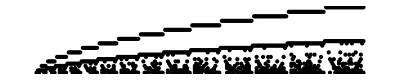

```mathematica
Graphics[Point[Flatten[Table[fracf[x],{x,1,255,1}],1]],ImageSize->Full]
```

## Roots 3D

```mathematica
fracf3D[x_,y_]:={x,y,#}&/@Keys@Select[#/Total@#&/@(Counts@ContinuedFraction[x^(1/y),dgts]),#>1/dgts&]
```

```mathematica
Flatten[Table[fracf3D[x,y],{x,1,3,1},{y,1,3,1}],2]
```

{{1,1,1},{1,2,1},{1,3,1},{2,1,2},{2,2,1},{2,2,2},{2,3,1},{2,3,3},{2,3,5},{2,3,4},{2,3,8},{2,3,14},{2,3,10},{2,3,2},{2,3,12},{2,3,15},{2,3,534},{2,3,121},{2,3,41},{2,3,7},{2,3,9},{2,3,6},{2,3,69},{2,3,89},{2,3,22},{2,3,186},{3,1,3},{3,2,1},{3,2,2},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,3,8},{3,3,9},{3,3,12},{3,3,11},{3,3,139},{3,3,52},{3,3,46},{3,3,20},{3,3,10}}

```mathematica
Off[ContinuedFraction::incomp,ContinuedFraction::terms]
maxy=3;maxx=10;
Manipulate[Graphics3D[Style[Point[fr=(Flatten[Table[fracf3D[x,y],{x,1,maxx,1},{y,1,maxy,1}],2])]],ImageSize->Large,PlotRange->Automatic,ViewPoint->{a}],{{a,Front,"View"},{Front,Right,Back,Left,Above,Below}}]
```

Table::iterb: Iterator {x,1,maxx,1} does not have appropriate bounds.

```mathematica
maxy=10;maxx=100;
Manipulate[Graphics3D[Table[Style[Point[fracf3D[x,y]],Hue[y/maxy,1,1,.7]],{x,1,maxx,1},{y,1,maxy,1}],PlotRange->Automatic,ImageSize->Large,ViewPoint->{a}],{{a,Front,"View"},{Front,Right,Back,Left,Above,Below}}]
```

Table::iterb: Iterator {x,1,maxx,1} does not have appropriate bounds.

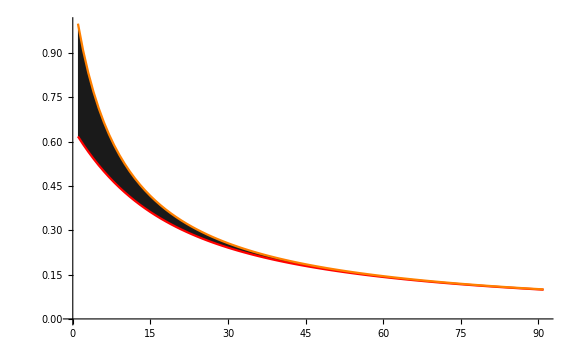

```mathematica
ListPlot[{Table[FromContinuedFraction[Table[n,1000]]-n//N,{n,1,10,.1}],
Table[x^-1,{x,1,10,.1}]},Joined->True,PlotRange->Full,PlotStyle->{Red,Orange},ImageSize->Large,Filling->{1-> {{2},GrayLevel[.1]}}]
```

```mathematica
Total@Table[x^-1,{x,1,10,.0001}]*.0001-Total@Table[FromContinuedFraction[Table[n,100]]-n//N,{n,1,10,.0001}]*.0001
```

0.285297

```mathematica
FromContinuedFraction[Table[Prime[n],{n,1,100}]]//N[#,10]&
```

2.313036736